```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
(************************** Definitions of Pnτ ***********************************)
```

```mathematica
Nn[R_,nn_]:=4/3 π R^3 nn
sigmaSat[R_,nn_]:=(π R^2)/Nn[R,nn]
tau[sigma_,R_,nn_]:=(3sigma)/(2sigmaSat[R,nn])
pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/Factorial[N] NIntegrate[y Exp[-y tau[sigma,R,nn]](y tau[sigma,R,nn])^N,{y,0,1}]
```

```mathematica
(*pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/(Factorial[N] tau[sigma,R,nn]^2)(Gamma[N+2]-Gamma[N+2,tau[sigma,R,nn]])*)
```

```mathematica
(* Numerical Values *)
```

```mathematica
vbar=287.8(*km/sec*);
vtilde=247(*km/sec*);
ηnum=√(3/(2 vbar^2))vtilde;
ρ0=0.3(*GeV/cc*);
Tsun=3 10^17; (*sec*)
```

```mathematica
fMBboosted[u_,η_,mdm_]:=ρ0/mdm(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2]Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)(*x=√(3/(2 vbar^2))u*)
```

```mathematica
β[mdm_,mN_]:=(4mN mdm)/(mN+mdm)^2
```

```mathematica
gN[u_,vesc_,N_,mdm_,mN_]:=1/β[mdm,mN] vesc^2/(vesc^2+u^2)((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-(1/β[mdm,mN]-1);
```

```mathematica
wΩminus[σ_,u_,vesc_,N_,n_,mdm_,mN_]:=σ n (u^2+vesc^2)gN[u,vesc,N,mdm,mN]
```

```mathematica
umin[vesc_,N_,mdm_,mN_]:=vesc √((1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1)-1)
```

```mathematica
umax[vesc_,N_,mdm_,mN_]:=vesc Sqrt[(1/(1-β[mdm,mN])(1/β[mdm,mN] Log[1/(1-β[mdm,mN])])^(N-1))-1]
```

```mathematica
cctomtrInv=10^6;
mtrtoKm=10^-3;
```

```mathematica
dCNdV[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,N_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mN_?NumericQ]:= π R^2 pn[σ,R,nn,N]NIntegrate[gN[u,vesc,N,mdm,mN] fMBboosted[u,ηnum,mdm]/u(u^2+vesc^2),{u,umin[vesc,N,mdm,mN],umax[vesc,N,mdm,mN]},MaxRecursion->12,WorkingPrecision->10](cctomtrInv/ mtrtoKm)
(* UNITS : R in mtr, u in km/sec, vesc in km/sec, mdm in GeV, ρ0 in Gev/cc, σ in m^2 *)
```

```mathematica
dCNdV[7 10^8,10^-44,600,5,10^30,10^4,25](* IF R in mtr then so is σ. Velocities are in km/sec *) (* The values correspond to SUN as of now *)
```

0.00110603

```mathematica
numdens[Mstar_,mp_,R_]:=1/(4/3 π R^3)Mstar/(2 mp);
```

```mathematica
n11=numdens[2 10^30,1.67 10^-27,0.07  10^8]
```

4.16774×10^35

```mathematica
sigmaSat[0.07 10^8,n11]
```

2.57077×10^-43

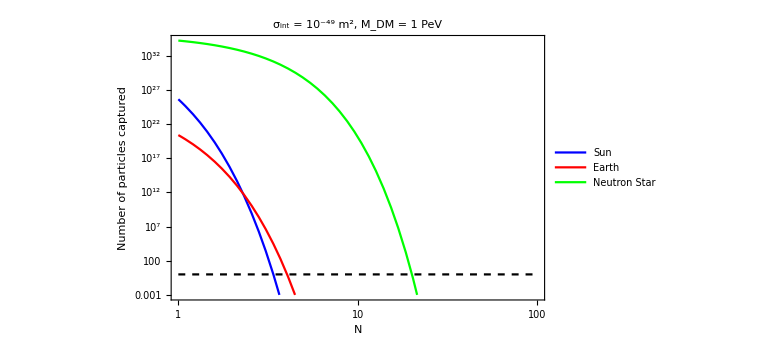

```mathematica
plotNmax1=LogLogPlot[{Tsun dCNdV[7 10^8,10^-49,618.0,x,4.1 10^29,10^6,1.0],Tsun dCNdV[6400000,10^-49,11.2,x,5.4 10^35,10^6,52],Tsun dCNdV[10^4,10^-49,10^5,x,10^44,10^6,1.0],1},{x,1,100},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Black,Dashed}},PlotRange->{Automatic,{0.001,Automatic}},Frame->True,FrameLabel->{Style["N",FontSize->20,Bold],Style["Number of particles captured",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"Sun","Earth","Neutron Star"},Top],PlotLabel->"σ_int = 10^-49 m^2, M_DM = 1 PeV"]
```

```mathematica
Export["nmax1.pdf",plotNmax1];
```

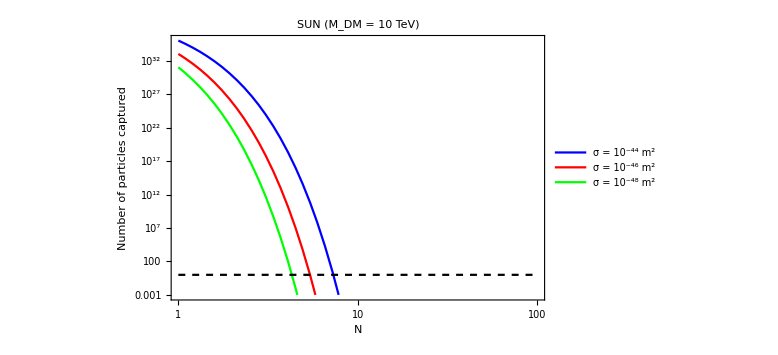

```mathematica
plotNmax2=LogLogPlot[{Tsun dCNdV[7 10^8,10^-44,618,x,10^30,10^4,1.0],Tsun dCNdV[7 10^8,10^-46,618,x,10^30,10^4,1.0],Tsun dCNdV[7 10^8,10^-48,618,x,10^30,10^4,1.0],1},{x,1,100},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick, Black, Dashed}},PlotRange->{Automatic,{0.001,Automatic}},Frame->True,FrameLabel->{Style["N",FontSize->20,Bold],Style["Number of particles captured",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-44 m^2","σ = 10^-46 m^2","σ = 10^-48 m^2"},Top],PlotLabel->"SUN (M_DM = 10 TeV)"]
```

```mathematica
Export["nmax2.pdf",plotNmax2];
```

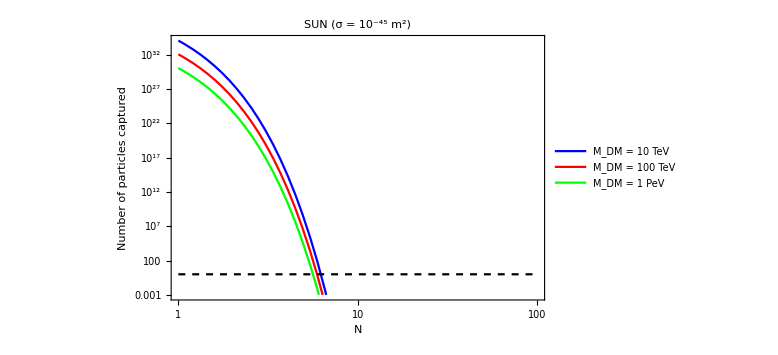

```mathematica
plotNmax3=LogLogPlot[{Tsun dCNdV[7 10^8,10^-45,618,x,10^30,10^4,1.0],Tsun dCNdV[7 10^8,10^-45,618,x,10^30,10^5,1.0],Tsun dCNdV[7 10^8,10^-45,618,x,10^30,10^6,1.0],1.0},{x,1,100},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Black,Dashed}},PlotRange->{Automatic,{0.001,Automatic}},Frame->True,FrameLabel->{Style["N",FontSize->20,Bold],Style["Number of particles captured",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"M_DM = 10 TeV","M_DM = 100 TeV", "M_DM = 1 PeV"},Top],PlotLabel->"SUN (σ = 10^-45 m^2)"]
```

```mathematica
Export["nmax3.pdf",plotNmax3];
```

```mathematica
(* little variation wrt Mdm but a bit more if σ is varied *)
```

```mathematica
(*Nmax[R_,σ_,vesc_,nn_,mdm_,mn_]:=x/.FindRoot[Tsun dCNdV[R,σ,vesc,x,nn,mdm,mn]==1.0,{x,1}]*)
```

```mathematica
Nmax[R_?NumericQ,σ_?NumericQ,vesc_?NumericQ,nn_?NumericQ,mdm_?NumericQ,mn_?NumericQ]:=For[Nsun=1,Nsun≤ 10^5,Nsun++,If[Tsun dCNdV[R,σ,vesc,Nsun,nn,mdm,mn]≤1,Return[Nsun];Break[]]];(*CAUTION : NEEDS to get cleared from the NSUN value before Running*)
```

```mathematica
Nmax[10^4,10^-46,10^5,10^44,10^7,1]
```

2

```mathematica
dCdVtot[R_,σ_,vesc_,nn_,mdm_?NumericQ,mn_]:=Sum[dCNdV[R,σ,vesc,n1,nn,mdm,mn],{n1,1,Nmax[R,σ,vesc,nn,mdm,mn]}]
```

```mathematica
dCdVtot[7 10^8,10^-44,618,10^30,10^5,1.0]
```

3.6222×10^15

```mathematica
dCdVtot[10^4,10^-46,10^5,10^44,10^6,1.0]//Timing
```

{5.76116,1.05039×10^15}

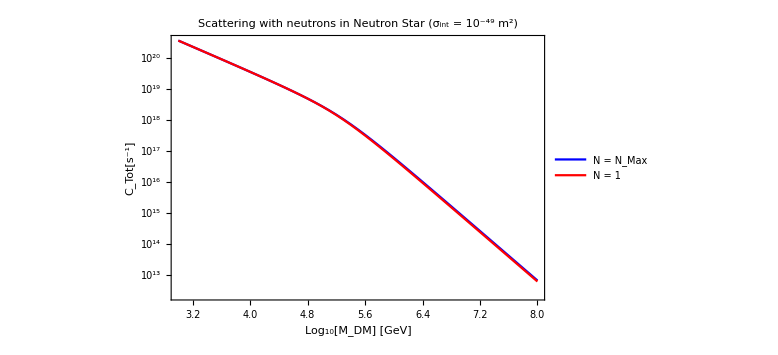

```mathematica
plotNeutron=ListLogPlot[{Table[{x,dCdVtot[10^4,10^-49,10^5,10^44,10^x,1.0]},{x,3,8,0.1}],Table[{x,dCNdV[10^4,10^-49,10^5,1,10^44,10^x,1.0]},{x,3,8,0.1}]},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,Joined-> True,FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["C_Tot[s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"N = N_Max","N = 1"},Top],PlotLabel->"Scattering with neutrons in Neutron Star (σ_int = 10^-49 m^2)"]
```

```mathematica
(*plotsun2=LogLogPlot[{dCdVtot[7 10^8,10^-44,618,10^30,x,1],dCdVtot[7 10^8,10^-46,618,10^30,x,1],dCdVtot[7 10^8,10^-48,618,10^30,x,1]},{x,10,10^4},PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},PlotRange->Automatic,Frame->True,FrameLabel->{Style["M_DM [GeV]",FontSize->20,Bold],Style["C_Tot [s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-44 m^2","σ = 10^-46 m^2","σ = 10^-48 m^2"},Top]]*)
```

```mathematica
(*plotsun2=LogPlot[dCdVtot[7 10^8,10^-45,618,10^30,10^x,1.0],{x,0,4},PlotStyle->{{Thick,Blue}},PlotRange->Automatic,Frame->True,FrameLabel->{Style["Log[M_DM [GeV]]",FontSize->20,Bold],Style["C_Tot [s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"σ = 10^-45 m^2"},Top]]*)
```

```mathematica
Export["plotNeutronStar.pdf",plotNeutron];
```

```mathematica
(*dCdVtotElec[R_,σ_,vesc_,nn_,mdm_,mn_]:=(val=0;For[i=1,i≤Nmax[R,σ,vesc,nn,mdm,mn],i++, val=dCNdV[R,σ,vesc,i,nn,mdm,mn]+val];Return[val]);*)
```

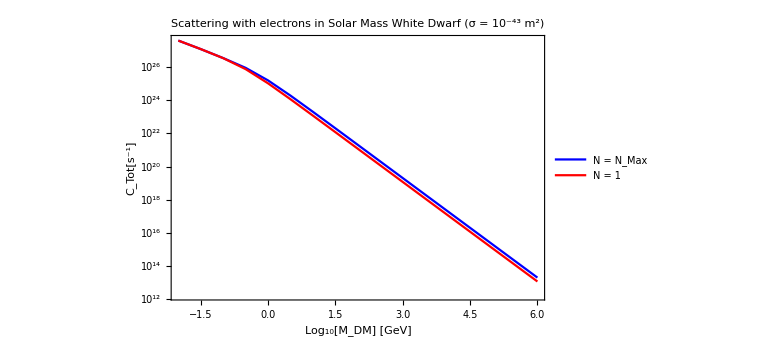

```mathematica
plotElecWD=ListLogPlot[{Table[{x,0.02dCdVtot[0.07 10^8,10^-43,6 10^3,10^36,10^x,0.5 10^-3]},{x,-2,6,0.5}],Table[{x,0.02dCNdV[0.07 10^8,10^-43,6 10^3,1,10^36,10^x,0.5 10^-3]},{x,-2,6,0.5}]},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,Joined-> True,AxesOrigin ->{-2,0},FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["C_Tot[s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"N = N_Max","N = 1"},Top],PlotLabel->"Scattering with electrons in Solar Mass White Dwarf (σ = 10^-43 m^2)"]
```

```mathematica
Export["ElecCompare2.pdf",plotElecWD];
```

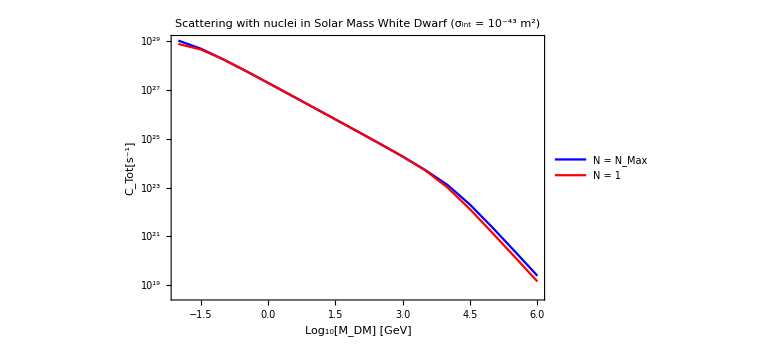

```mathematica
plotElecWD3=ListLogPlot[{Table[{x,dCdVtot[0.07 10^8,10^-43,6 10^3,10^36,10^x,12.0]},{x,-2,6,0.5}],Table[{x,dCNdV[0.07 10^8,10^-43,6 10^3,1,10^36,10^x,12.0]},{x,-2,6,0.5}]},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotRange->Automatic,Frame->True,Joined-> True,AxesOrigin ->{-2,Automatic},FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["C_Tot[s^-1]",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],ImageSize->Large,PlotLegends->Placed[{"N = N_Max","N = 1"},Top],PlotLabel->"Scattering with nuclei in Solar Mass White Dwarf (σ_int = 10^-43 m^2)"]
```

```mathematica
Export["ElecCompare3.pdf",plotElecWD3];
```